```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

596

596

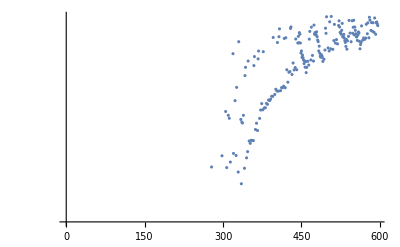

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{8*^4,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|Q1EkG→164.269,Q2EkG→-160.031,Q3EkG→108.433,Q4EkG→133.028,Q5EkG→-23.6701,Q6EkG→-144.885,S1ELkG→879.633,S2ELkG→-1863.71,S3ELkG→-912.494,S3ERkG→-1173.73,S2ERkG→-1835.83,S1ERkG→920.844,Q5FFkG→-72.561,Q4FFkG→-81.2099,Q3FFkG→99.1016,Q2FFkG→126.388,Q1FFkG→-235.04,Q0FFkG→126.719,PDrive_mean_x→3.4613×10^-6,PDrive_mean_y→6.393×10^-7,PDrive_sigma_x→0.000146497,PDrive_sigma_y→0.000052509,PDrive_mean_xp→0.0000961281,PDrive_mean_yp→2.033×10^-7,PDrive_sigmaSI90_x→0.000121348,PDrive_sigmaSI90_y→0.0000337052,PDrive_emitSI90_x→0.000351329,PDrive_emitSI90_y→4.0401×10^-6,PDrive_zLen→0.0000407025,PDrive_zCentroid→991.332,PWitness_mean_x→-1.413×10^-6,PWitness_mean_y→-2.9527×10^-6,PWitness_sigma_x→0.0000342341,PWitness_sigma_y→0.0000357996,PWitness_mean_xp→-0.0000801253,PWitness_mean_yp→-7.049×10^-7,PWitness_sigmaSI90_x→0.0000286385,PWitness_sigmaSI90_y→0.0000284579,PWitness_emitSI90_x→0.0000600762,PWitness_emitSI90_y→3.4001×10^-6,PWitness_zLen→0.0000157046,PWitness_zCentroid→991.332,bunchSpacing→0.000155183,transverseCentroidOffset→6.0549×10^-6,lostChargeFraction→0.,maximizeMe→98889.|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

Q1EkG : 164.2691038795
Q2EkG : -160.0313998078
Q3EkG : 108.4325815396
Q4EkG : 133.027921079
Q5EkG : -23.6700528705
Q6EkG : -144.8854845082
S1ELkG : 879.6325654359
S2ELkG : -1863.7105990745
S3ELkG : -912.4937325211
S3ERkG : -1173.7251948869
S2ERkG : -1835.8279833315
S1ERkG : 920.8442962838
Q5FFkG : -72.5610135339
Q4FFkG : -81.2099307402
Q3FFkG : 99.1015564951
Q2FFkG : 126.3879648788
Q1FFkG : -235.0400508137
Q0FFkG : 126.7187578988
PDrive_mean_x : 3.4613e-6
PDrive_mean_y : 6.393e-7
PDrive_sigma_x : 0.0001464965
PDrive_sigma_y : 0.000052509
PDrive_mean_xp : 0.0000961281
PDrive_mean_yp : 2.033e-7
PDrive_sigmaSI90_x : 0.0001213482
PDrive_sigmaSI90_y : 0.0000337052
PDrive_emitSI90_x : 0.0003513293
PDrive_emitSI90_y : 4.0401e-6
PDrive_zLen : 0.0000407025
PDrive_zCentroid : 991.3316912304
PWitness_mean_x : -1.413e-6
PWitness_mean_y : -2.9527e-6
PWitness_sigma_x : 0.0000342341
PWitness_sigma_y : 0.0000357996
PWitness_mean_xp : -0.0000801253
PWitness_mean_yp : -7.049e-7
PWitness_sigmaSI90_x : 0.0000286385
PWitness_sigmaSI90_y : 0.0000284579
PWitness_emitSI90_x : 0.0000600762
PWitness_emitSI90_y : 3.4001e-6
PWitness_zLen : 0.0000157046
PWitness_zCentroid : 991.3318464138
bunchSpacing : 0.0001551834
transverseCentroidOffset : 6.0549e-6
lostChargeFraction : 0.
maximizeMe : 98888.9961577755

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

6.05485×10^-6

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG"}
]
```

{Q0FFkG,Q1EkG,Q1FFkG,Q2EkG,Q2FFkG,Q3EkG,Q3FFkG,Q4EkG,Q4FFkG,Q5EkG,Q5FFkG,Q6EkG,S1ELkG,S1ERkG,S2ELkG,S2ERkG,S3ELkG,S3ERkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVars,
Symbol[#]&/@freeVars
]
```

FittedModel[…]

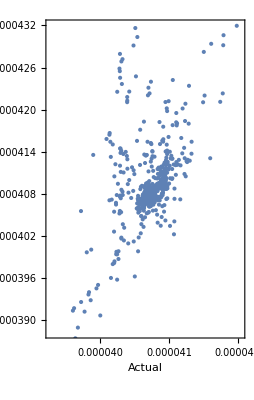

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVars
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{Q0FFkG→Indeterminate,Q1EkG→Indeterminate,Q1FFkG→Indeterminate,Q2EkG→Indeterminate,Q2FFkG→Indeterminate,Q3EkG→Indeterminate,Q3FFkG→Indeterminate,Q4EkG→Indeterminate,Q4FFkG→Indeterminate,Q5EkG→Indeterminate,Q5FFkG→Indeterminate,Q6EkG→Indeterminate,S1ELkG→Indeterminate,S1ERkG→Indeterminate,S2ELkG→Indeterminate,S2ERkG→Indeterminate,S3ELkG→Indeterminate,S3ERkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
Q0FFkG | 1 | 2.86089×10^-11 | 2.86089×10^-11 | 7.93138 | 0.00502463
Q1EkG | 1 | 1.5691×10^-11 | 1.5691×10^-11 | 4.3501 | 0.0374456
Q1FFkG | 1 | 7.08052×10^-11 | 7.08052×10^-11 | 19.6296 | 0.0000112502
Q2EkG | 1 | 1.15911×10^-9 | 1.15911×10^-9 | 321.345 | 1.8793×10^-57
Q2FFkG | 1 | 5.21517×10^-11 | 5.21517×10^-11 | 14.4583 | 0.000158559
Q3EkG | 1 | 1.18729×10^-9 | 1.18729×10^-9 | 329.156 | 1.53411×10^-58
Q3FFkG | 1 | 6.75587×10^-11 | 6.75587×10^-11 | 18.7296 | 0.0000177551
Q4EkG | 1 | 1.82276×10^-9 | 1.82276×10^-9 | 505.331 | 7.44879×10^-81
Q4FFkG | 1 | 3.51803×10^-11 | 3.51803×10^-11 | 9.75318 | 0.00187986
Q5EkG | 1 | 4.56247×10^-12 | 4.56247×10^-12 | 1.26487 | 0.261198
Q5FFkG | 1 | 2.20611×10^-11 | 2.20611×10^-11 | 6.1161 | 0.0136825
Q6EkG | 1 | 2.55128×10^-12 | 2.55128×10^-12 | 0.707304 | 0.400689
S1ELkG | 1 | 2.25511×10^-12 | 2.25511×10^-12 | 0.625195 | 0.429448
S1ERkG | 1 | 2.26614×10^-11 | 2.26614×10^-11 | 6.28252 | 0.0124674
S2ELkG | 1 | 6.00064×10^-11 | 6.00064×10^-11 | 16.6358 | 0.0000516558
S2ERkG | 1 | 6.82981×10^-13 | 6.82981×10^-13 | 0.189346 | 0.663624
S3ELkG | 1 | 3.07798×10^-15 | 3.07798×10^-15 | 0.000853323 | 0.976706
S3ERkG | 1 | 2.3997×10^-12 | 2.3997×10^-12 | 0.665279 | 0.415039
Error | 577 | 2.08127×10^-9 | 3.60706×10^-12 |  | 
Total | 595 | 6.6376×10^-9 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVars,
Symbol[#]&/@freeVars
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];
```

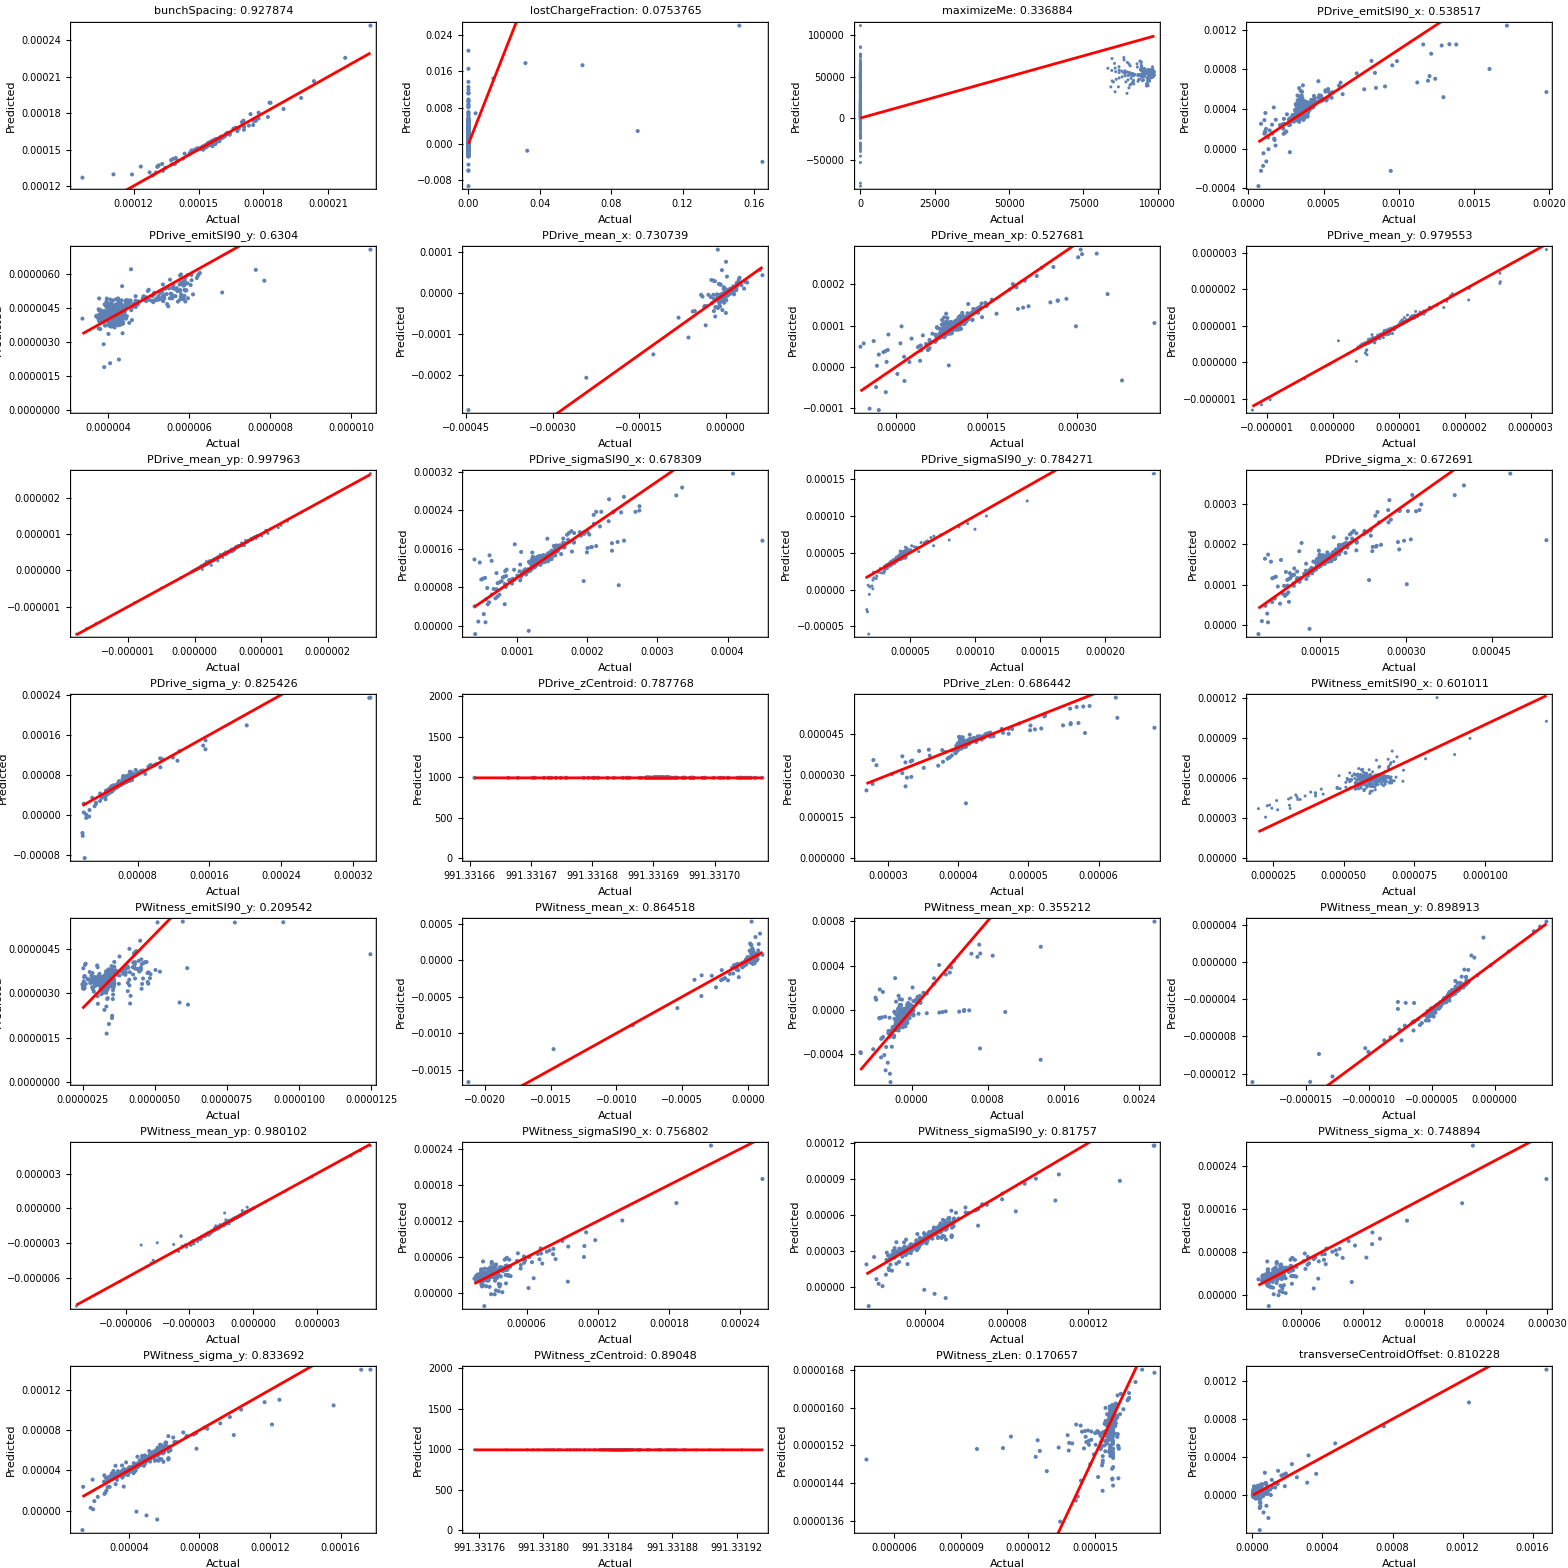

```mathematica
displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```